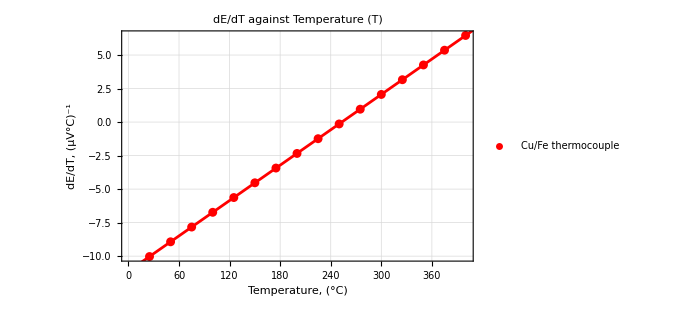
-Graphics-
Cu/Fe thermocouple: y==0.0439629 x-11.1278, Uncertainty in Slope: 5.85287×10^-6

```mathematica
(*Define the datasets*)
t1={{25,-10.03},{50,-8.93},{75,-7.83},{100,-6.73},{125,-5.63},{150,-4.53},{175,-3.43},{200,-2.34},{225,-1.24},{250,-0.14},{275,0.96},{300,2.06},{325,3.16},{350,4.26},{375,5.36},{400,6.46}};

t1error={{Around[25,1],Around[-10.03,0.01]},{Around[50,1],Around[-8.93,0.01]},{Around[75,1],Around[-7.83,0.01]},{Around[100,1],Around[-6.73,0.01]},{Around[125,1],Around[-5.63,0.01]},{Around[150,1],Around[-4.53,0.01]},{Around[175,1],Around[-3.43,0.01]},{Around[200,1],Around[-2.34,0.01]},{Around[225,1],Around[-1.24,0.01]},{Around[250,1],Around[-0.14,0.01]},{Around[275,1],Around[0.96,0.01]},{Around[300,1],Around[2.06,0.01]},{Around[325,1],Around[3.16,0.01]},{Around[350,1],Around[4.26,0.01]},{Around[375,1],Around[5.36,0.01]},{Around[400,1],Around[6.46,0.01]}};

(*Fit linear models to the data*)
fitt1=LinearModelFit[t1,x,x];

(*Extracting uncertainties in the slope of each fit*)uncertainty1=fitt1["ParameterTableEntries"][[2,2]];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitt1["BestFit"]]];

(*Existing code for plotting*)Column[{combinedPlot=Show[ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fitt1[x]},{x,0,420},PlotStyle->{Red}],Frame->True,FrameLabel->{"Temperature, (°C)","dE/dT, (µV°C)^-1"},GridLines->Automatic,PlotLabel->"dE/dT against Temperature (T)",ImageSize->500];
(*Displaying the results*)Column[{combinedPlot,Row[{"Cu/Fe thermocouple: ",eq1,", Uncertainty in Slope: ",uncertainty1}]}]
}
]
```